```mathematica
Needs["Histograms`"]
Needs["HypothesisTesting`"]
holidays = 7;
```

General::obspkg: Histograms` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

BarChart3D::shdw: Symbol BarChart3D appears in multiple contexts BarCharts`System`; definitions in context BarCharts` may shadow or be shadowed by other definitions.

Histogram3D::shdw: Symbol Histogram3D appears in multiple contexts Histograms`System`; definitions in context Histograms` may shadow or be shadowed by other definitions.

MeanCI::shdw: Symbol MeanCI appears in multiple contexts HypothesisTesting`Global`; definitions in context HypothesisTesting` may shadow or be shadowed by other definitions.

α = 0.00335578

σ = 0.0394339

annual income = 134. %

n = 138.088

{0.000584082,0.00612747}

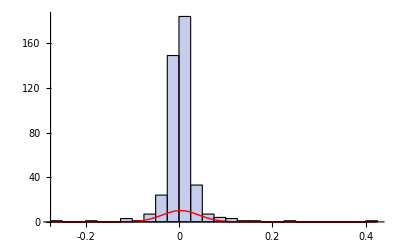

p = 0.0188086

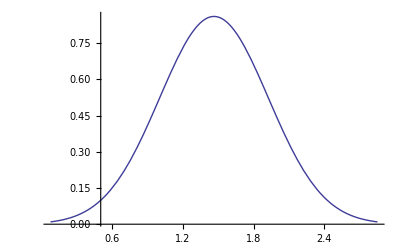

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {x} = {0.999`}.

ReplaceAll::reps: {FindRoot[cl[x] == 0, {x, 0.999`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ConfidenceLevel = x/.FindRoot[cl[x]==0,{x,0.999}]

```mathematica
coefVolume = 1;
initDeposit = 15000000;
data0 = {0,-98940,-238150,49370,427710,167320,-112570,-446600,-80930,-500140,-377190,-1449950,-1541080,244200,237830,1139510,1107260,1635160,1679590,1819450,1219440,937540,832960,146680,416190,402610,-386130,-61120,-1223140,-2939110,-2808470,-6159090,-6398990,-2788580,-2150140,-2006090,-1986090,-1987290,-2437880,-3846100,-5905180,-4919030,-4319820,-1781700,-286110,-33110,-297330,-1315910,-713520,1534560,2126380,1410560,1637870,1191010,1426610,736500,1624700,2138510,3863520,3684180,4075330,4742660,5114160,4056510,4802620,4156560,4602260,6214150,7110460,7462960,7704810,7943240,7868880,7405420,8201640,7938330,7038610,7518670,7734420,7004680,7984180,8550330,6933800,6075490,3623390,3443110,3762020,4928710,4069690,4637340,6581700,8575800,8335270,8224540,8983620,9498190,10399630,10140230,10314130,10409500,10603340,10521230,10570310,10746150,11156500,10575770,10575770,10502570,10600040,10338090,10580330,10758860,10749520,10720910,10752510,10656800,10818590,10700050,10656040,10711870,10935290,11163600,11127220,11191250,11092560,11115880,11206070,11046890,11376250,10542260,10160010,9208560,10307950,10810100,10723210,10869390,11480600,11443300,11543130,10952250,11051900,11156110,10546240,10561470,10145990,10906690,10389120,11185590,12006110,12122930,11021680,11979680,11653400,11252100,11978620,12077520,12959200,13109960,15032360,14568000,15247710,15632140,16021390,16322840,16296260,16343380,16210980,16141720,15638440,15797530,16174400,16352190,15882480,15804800,15701430,15858820,16600820,17501980,17624640,17751590,17764570,17791690,17397580,15322900,17732260,18113800,17856880,18874570,19740080,20371420,21108020,21232980,21141660,20515920,20697700,20643860,20698500,20874350,20808960,20993590,21503500,20985360,21332640,21508700,21524740,21393760,21664150,21758750,21779500,21827530,21686100,22370770,22370770,22318270,22346860,22304190,22263390,22256320,22251820,22228240,22353200,22535630,22640490,22580260,22707690,22709210,22609380,22550080,22471590,22539330,22253350,22409300,22830560,21971680,22068990,21932210,21716140,21863910,22901220,22907580,22765630,20773350,20247290,20069940,19839520,21855210,21904100,22130080,21916590,22501760,22377630,21406530,21484240,20180590,20221860,19935010,18798020,18762500,19379110,19123610,20606170,20912470,20252340,19507880,19828600,20466800,21252390,21272690,20497420,21433280,21356620,20957940,19902550,19919450,20568620,19524140,19632970,19721320,20966510,21248890,20911450,20696710,21488460,21663790,20640660,20725670,20646510,20266130,20808990,20474160,21086450,21730560,22509760,22198360,21842550,22645950,24527570,24986950,24782700,23642080,23923050,23824200,23466770,23502900,23909010,25788090,24799820,24562620,25637160,25555710,24661370,25260060,25332440,25214850,25214850,25117560,25521940,25576090,25690010,25502840,25299000,25244310,25505770,24631560,24814530,23099120,24162770,24124200,24212030,24920130,24520400,26329650,26141100,26296550,26410110,26279790,26432710,26396330,26229040,26100960,26155590,26649130,27015690,27515200,27524510,27823050,27896660,28020600,28274940,28439320,28139780,27943700,27897000,28062920,27915030,28377130,27792780,28021240,27576040,27724750,28003790,28421990,28489510,28506160,28290550,29061980,28974130,29468350,29900640,29935540,30133000,30298440,30145190,29938180,29917140,30003570,30473530,30600500,30240980,30378170,31010140,31009650,30838420,31212040,31428520,30949290,30676890,30633790,30197290,30207980,30484040,30614720,30402780,30405380,30862920,31240280,31585340,32015500,31961640,32039750,31489780,32083540,32298530,32027200,31665590,31774090,31538280,30840920,31403610,31040750,31959940,32166040,31055800,30001480,30998200,30681510,31263410,31544910,30626360,29626230,30319940,29939140}*coefVolume +initDeposit;
If[Min[data0]<initDeposit/3, Print["STOPPPPPPPPPPPPPP"]];
p0 = Table[N[data0[[i]]/data0[[i-1]]],{i, 2, Length[data0]}];
p = p0;
p = p -1;
n = Length[p];
g0 =Histogram[p];
α = Mean[p];
σ = StandardDeviation[p];
Print["α = ", α];
Print["σ = ", σ];
Print["annual income = ",Round[100( (1 + α)^(365 * 5/7-holidays)-1), 0.1], " %"];
g1 = Plot[1/(√(2 π)σ)Exp[-(x - α)^2/(2 σ^2)], {x, Min[p], Max[p]}, PlotRange->All, PlotStyle->RGBColor[1, 0, 0]];
n = (σ/α)^2;
Print["n = ", n];
a = 1 + α n - 3 σ √n;
b = 1 + α n + 3 σ √n;
Print[MeanCI[p, ConfidenceLevel->0.85]];
(* find confidence level for non negative interval *)
Print[Show[g0, g1]];
f = 1/(√(2 π n)σ)Exp[-(1 + α n - x)^2/(2 σ^2 n)];
p = ∫_(-∞)^(1/2) fⅆx;
Print["p = ", p];
Plot[f,{x, a, b}, PlotRange->All]
cl[x_]:=MeanCI[p, ConfidenceLevel->x][[1]];
x0 = FindRoot[cl[x] == 0, {x, 0.999}];
Print["ConfidenceLevel = ", x/.x0];
```